Hub-and-Spoke Network

Variables

```mathematica
runtime = 36;
p=4;
ein=5;
w=0.1;
```

Number of Entities

```mathematica
NA=3; (* number of Hubs *)
NB1=32;(* number of C suppliers  Hub 1*)
NB2=54;(* number of C suppliers  Hub 2*)
NB3=75;(* number of C suppliers Hub 3*)
```

#### Natural Frequencies

```mathematica
ωOEM =12.08; (* OEM *)
ωA1=12.08;(* Hub 1 *)
ωA2=14.31;(* Hub 2 *)
ωA3=13.09;(* Hub 3 *)
ωBR=Abs[RandomVariate[NormalDistribution[4.43,0.46],NB1]]; (* C supplier  Hub 1*)
ωBN=Abs[RandomVariate[NormalDistribution[13.84,0.23],NB2]]; (* C supplier Hub 2*)
ωBI=Abs[RandomVariate[NormalDistribution[3.75,0.56],NB3]]; (* C supplier Hub 3*)
```

Coupling

```mathematica
KOEMA=KAOEM=0;
KAB1=KBA1=1/NB1;
KAB2=KBA2=1/NB2;
KAB3=KBA3=1/NB3;
KHUB=0.70;(* Vernetzungsgrad milk-run*)
```

Vernetzungsgrad

```mathematica
V=0.0;(* Vernetzungsgrad zwischen den Hubs*)
```

Oscillator Equations

```mathematica
de1=NDSolve[{
(* car manufacturer *)
θ0[1]'[t]==ωOEM- Sum[KOEMA Sin[θ0[1][t]-θ1r[n][t]],{n,NA}],

(* Hub 1*)
θ1r[1]'[t]==ωA1-KAOEM Sin[θ1r[1][t]-θ0[1][t]]- Sum[KAB1 Sin[θ1r[1][t]-θ2r[m][t]],{m,NB1}]- V(0.5(Sin[θ1r[1][t]-θ1r[2][t]]+Sin[θ1r[1][t]-θ1r[3][t]])),

(* Hub 2*)
θ1r[2]'[t]==ωA2-KAOEM Sin[θ1r[2][t]-θ0[1][t]]- Sum[ KAB2 Sin[θ1r[2][t]-θ2n[m][t]],{m,NB2}]- V(0.5(Sin[θ1r[2][t]-θ1r[1][t]]+Sin[θ1r[2][t]-θ1r[3][t]])),

(* Hub 3*)
θ1r[3]'[t]==ωA3-KAOEM Sin[θ1r[3][t]-θ0[1][t]]- Sum[ KAB3 Sin[θ1r[3][t]-θ2i[m][t]],{m,NB3}]- V(0.5(Sin[θ1r[3][t]-θ1r[1][t]]+Sin[θ1r[3][t]-θ1r[2][t]])),

(* C supplier Hub 1*)
Table[{θ2r[n]'[t]==ωBR[[n]]
- KBA1 Sin[θ2r[n][t]-θ1r[1][t]]-KHUB Sum[ KBA1 Sin[θ2r[n][t]-θ2r[s][t]],{s,NB1}]},{n,NB1}],

(* C supplier Hub 2 *)
Table[{θ2n[n]'[t]==ωBN[[n]]
-KBA2 Sin[θ2n[n][t]-θ1r[2][t]]- KHUB Sum[ KBA2 Sin[θ2n[n][t]-θ2n[s][t]],{s,NB2}]},{n,NB2}],

(* C supplier Hub 3 *)
Table[{θ2i[n]'[t]==ωBI[[n]]
-KBA3 Sin[θ2i[n][t]-θ1r[3][t]]-KHUB Sum[ KBA3 Sin[θ2i[n][t]-θ2i[s][t]],{s,NB3}]},{n,NB3}],

Table[θ1r[n][0]==0,{n,NA}],Table[θ2r[n][0]==0,{n,NB1}],Table[θ2n[n][0]==0,{n,NB2}],Table[θ2i[n][0]==0,{n,NB3}],θ0[1][0]==0},
Join[Table[θ1r[n],{n,NA}],Table[θ2r[n],{n,NB1}],Table[θ2n[n],{n,NB2}],Table[θ2i[n],{n,NB3}],{θ0[1]}], {t,0,runtime}];
```

___________________________________________________________________________________________________________

```mathematica
Results
```

Results

```mathematica
r1=Sum[Exp[I  θ1r[n][t]],{n,NA}]/NA; l1 =Abs[r1];w1 =Arg[r1]; 
r5=Sum[Exp[I  θ2r[n][t]],{n,NB1}]/NB1;l5 =Abs[r5];w5 =Arg[r5]; 
r6=Sum[Exp[I  θ2n[n][t]],{n,NB2}]/NB2;l6 =Abs[r6];w6 =Arg[r6]; 
r7=Sum[Exp[I  θ2i[n][t]],{n,NB3}]/NB3;l7 =Abs[r7];w7 =Arg[r7]; 

RAV1=Sum[l1,{t,ein,runtime}]/(runtime-ein);
RAV5=Sum[l5,{t,ein,runtime}]/(runtime-ein);
RAV6=Sum[l6,{t,ein,runtime}]/(runtime-ein);
RAV7=Sum[l7,{t,ein,runtime}]/(runtime-ein);

R1=Evaluate [RAV1/.de1];
R5=Evaluate [RAV5/.de1];R6=Evaluate [RAV6/.de1];R7=Evaluate [RAV7/.de1];
```

```mathematica
data={{R1,R5,R6,R7}};
Text@Grid[Prepend[data,{"Hub1-3","C-Hub1","C-Hub2","C-Hub1"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->{{Left,{Center}}},ItemSize->{{8,8,8,8,8,8,8}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

Hub1-3 | C-Hub1 | C-Hub2 | C-Hub1
{0.562942} | {0.347878} | {0.977594} | {0.233361}

_____________________________________________________________________________________________________________________________

```mathematica
CI=ParametricPlot[{Cos[x],Sin[x]},{x,0,2π},Axes->None, PlotStyle->{Medium,Brown,Dotted}]
```

-Graphics-

Hub1-3

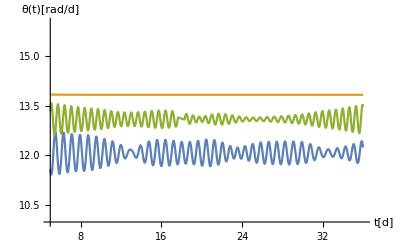

```mathematica
Plot[Evaluate [Table[θ1r[n]'[t],{n,NA}]/.de1],{t,ein,runtime},PlotRange->{{ein,runtime},{10,16}},LabelStyle->{FontFamily->"Calibri",14,Black},AxesLabel->{"t[d]","θ̇(t)[rad/d]"},PlotStyle->ColorData[97,"ColorList"]]
```

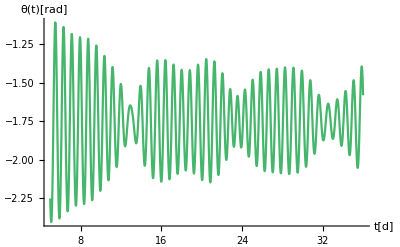

```mathematica
Plot[Evaluate [(θ1r[1]'[t]-θ1r[2]'[t])/.de1],{t,ein,runtime},PlotRange->{{ein,runtime},All},LabelStyle->{FontFamily->"Calibri",14,Black},AxesLabel->{"t[d]","θ̇(t)[rad]"},PlotStyle->ColorData[97,"ColorList"]]
```

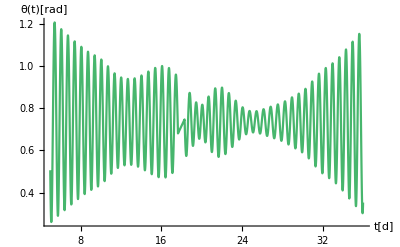

```mathematica
Plot[Evaluate [θ1r[2]'[t]-θ1r[3]'[t]/.de1],{t,ein,runtime},PlotRange->{{ein,runtime},All},LabelStyle->{FontFamily->"Calibri",14,Black},AxesLabel->{"t[d]","θ̇(t)[rad]"},PlotStyle->ColorData[97,"ColorList"]]
```

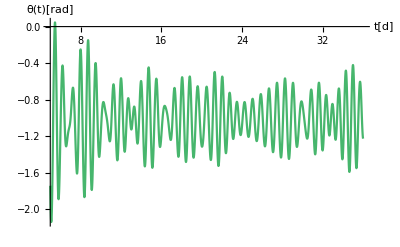

```mathematica
Plot[Evaluate [θ1r[1]'[t]-θ1r[3]'[t]/.de1],{t,ein,runtime},PlotRange->{{ein,runtime},All},LabelStyle->{FontFamily->"Calibri",14,Black},AxesLabel->{"t[d]","θ̇(t)[rad]"},PlotStyle->ColorData[97,"ColorList"]]
```

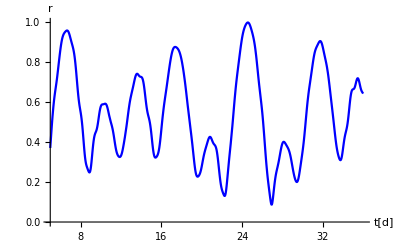

```mathematica
A=Plot[l1/.de1, {t,5,runtime},LabelStyle->{FontFamily->"Calibri",18,Black},PlotRange->{{5,runtime},{0,1.0}},MaxRecursion->p,AxesLabel->{"t[d]","r"},PlotStyle->Directive[Blue]]
```

```mathematica
P1=Table[Phasor1=Sum[Evaluate[θ1r[n]'[t]]/.de1,{t,ein,runtime}]/(runtime-ein),{n,NA}]
```

{{12.4548},{14.2705},{13.5188}}

```mathematica
P[[2,1]]
```

Part::partd: Part specification P⟦2,1⟧ is longer than depth of object.

P⟦2,1⟧

```mathematica
A=ListPlot[{Table[{Cos[P1[[m,1]]],Sin[P1[[m,1]]]},{m,NA}]},Axes->False,Frame->True,FrameLabel->{"Re(z_i)","Im(z_i)"},LabelStyle->{FontFamily->"Calibri",28,Black},PlotStyle->Directive[PointSize[0.05]],PlotRange->{{-1.1,1.1},{-1.1,1.1}},AspectRatio->1,ColorFunction->Function[{m},Hue[1,1,m]]];
```

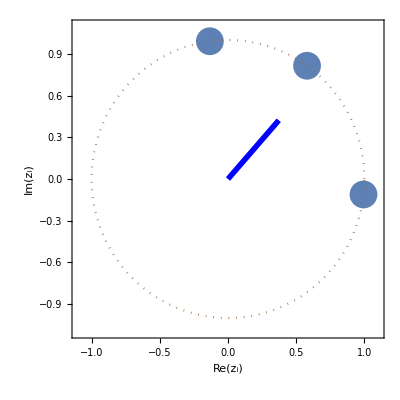

```mathematica
D1=R1[[1]]Cos [Sum[P1[[n,1]],{n,NA}]/NA];
D2=R1[[1]]Sin [Sum[P1[[n,1]],{n,NA}]/NA];
AA=Graphics[{Blue,Thickness[0.01],Arrow[{{0,0},{D1,D2}}]}];
Show[A,CI,AA]
```

Hub 1 to C-supplier cluster 1

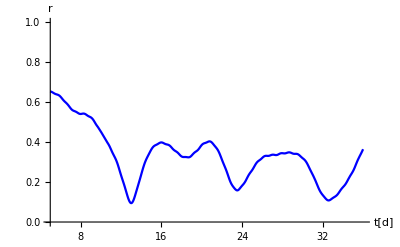

```mathematica
Plot[l5/.de1, {t,ein,runtime},LabelStyle->{FontFamily->"Calibri",18,Black},PlotRange->{{5,runtime},{0,1.0}},MaxRecursion->p,AxesLabel->{"t[d]","r"},PlotStyle->Directive[Blue]]
```

```mathematica
P2=Table[Phasor2=Sum[Evaluate[θ2r[n]'[t]]/.de1,{t,ein,runtime}]/(runtime-ein),{n,NB1}];
```

```mathematica
AB1=ListPlot[{Table[{Cos[P2[[m,1]]],Sin[P2[[m,1]]]},{m,NB1}]},Axes->False,Frame->True,FrameLabel->{"Re(z_i)","Im(z_i)"},LabelStyle->{FontFamily->"Calibri",28,Black},PlotStyle->Directive[PointSize[0.05]],PlotRange->{{-1.1,1.1},{-1.1,1.1}},AspectRatio->1,ColorFunction->Function[{m},Hue[1,1,m]]];
```

-0.0812811

-0.338249

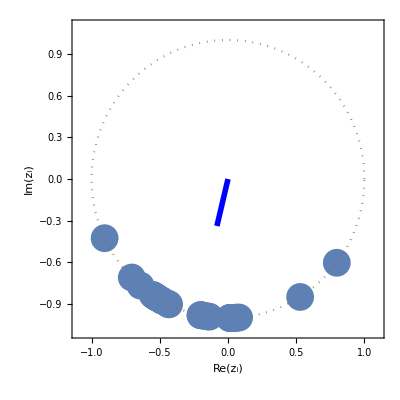

```mathematica
D3=R5[[1]]Cos [Sum[P2[[m,1]],{m,NB1}]/NB1]
D4=R5[[1]]Sin [Sum[P2[[m,1]],{m,NB1}]/NB1]
KK=Graphics[{Blue,Thickness[0.01],Arrow[{{0,0},{D3,D4}}]}];
Show[AB1,CI,KK]
```

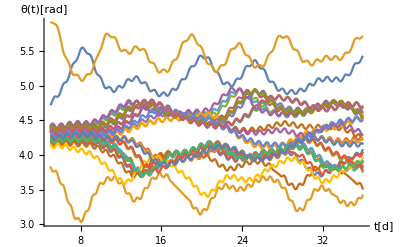

```mathematica
K1=Plot[Evaluate [Table[θ2r[n]'[t],{n,NB1}]/.de1],{t,ein,runtime},PlotRange->{{5,runtime},All},LabelStyle->{FontFamily->"Calibri",18,Black},AxesLabel->{"t[d]"," θ̇(t)[rad]"},MaxRecursion->p]
```

Hub 2 to C-supplier cluster 2

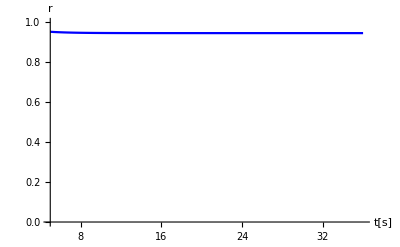

```mathematica
Plot[l6/.de1, {t,ein,runtime},LabelStyle->{FontFamily->"Calibri",18,Black},PlotRange->{{5,runtime},{0,1.0}},MaxRecursion->p,AxesLabel->{"t[s]","r"},PlotStyle->Directive[Blue]]
```

```mathematica
P3=Table[Phasor3=Sum[Evaluate[θ2n[m]'[t]]/.de1,{t,ein,runtime}]/(runtime-ein),{m,NB2}];
```

```mathematica
AB2=ListPlot[{Table[{Cos[P3[[m,1]]],Sin[P3[[m,1]]]},{m,NB2}]},Axes->False,Frame->True,FrameLabel->{"Re(z_i)","Im(z_i)"},LabelStyle->{FontFamily->"Calibri",28,Black},PlotStyle->Directive[PointSize[0.05]],PlotRange->{{-1.1,1.1},{-1.1,1.1}},AspectRatio->1,ColorFunction->Function[{m},Hue[1,1,m]]];
```

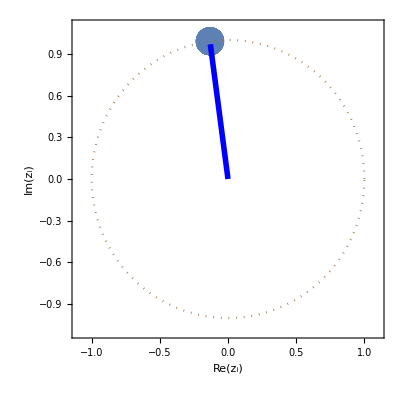

```mathematica
D5=R6[[1]]Cos [Sum[P3[[n,1]],{n,NB2}]/NB2];
D6=R6[[1]]Sin [Sum[P3[[n,1]],{n,NB2}]/NB2];
LL=Graphics[{Blue,Thickness[0.01],Arrow[{{0,0},{D5,D6}}]}];
Show[AB2,CI,LL]
```

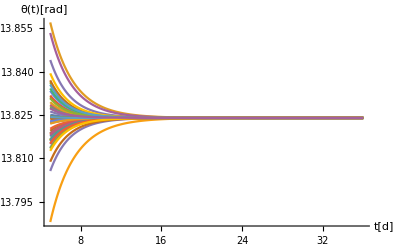

```mathematica
Plot[Evaluate [Table[θ2n[n]'[t],{n,NB2}]/.de1],{t,ein,runtime},PlotRange->{{5,runtime},All},LabelStyle->{FontFamily->"Calibri",18,Black},AxesLabel->{"t[d]","θ̇(t)[rad]"},MaxRecursion->p]
```

Hub 3 to C-supplier cluster 3

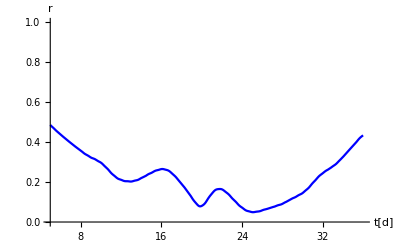

```mathematica
Plot[l7/.de1, {t,ein,runtime},LabelStyle->{FontFamily->"Calibri",18,Black},PlotRange->{{5,runtime},{0,1.0}},MaxRecursion->p,AxesLabel->{"t[d]","r"},PlotStyle->Directive[Blue]]
```

```mathematica
P4=Table[Phasor4=Sum[Evaluate[θ2i[m]'[t]]/.de1,{t,ein,runtime}]/(runtime-ein),{m,NB3}];
```

```mathematica
AB3=ListPlot[{Table[{Cos[P4[[m,1]]],Sin[P4[[m,1]]]},{m,NB3}]},Axes->False,Frame->True,FrameLabel->{"Re(z_i)","Im(z_i)"},LabelStyle->{FontFamily->"Calibri",28,Black},PlotStyle->Directive[PointSize[0.05]],PlotRange->{{-1.1,1.1},{-1.1,1.1}},AspectRatio->1,ColorFunction->Function[{m},Hue[1,1,m]]];
```

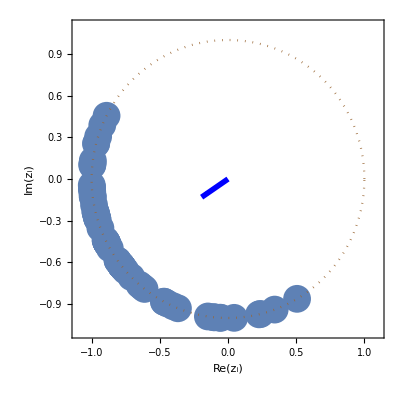

```mathematica
D7=R7[[1]]Cos [Sum[P4[[n,1]],{n,NB3}]/NB3];
D8=R7[[1]]Sin [Sum[P4[[n,1]],{n,NB3}]/NB3];
HH=Graphics[{Blue,Thickness[0.01],Arrow[{{0,0},{D7,D8}}]}];
Show[AB3,CI,HH]
```

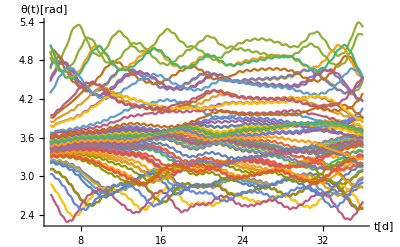

```mathematica
Plot[Evaluate [Table[θ2i[n]'[t],{n,NB3}]/.de1],{t,ein,runtime},PlotRange->{{5,runtime},All},LabelStyle->{FontFamily->"Calibri",18,Black},AxesLabel->{"t[d]","θ̇(t)[rad]"},MaxRecursion->p]
```

```mathematica
ClearAll;
```